```mathematica
bin=-Graphics-
```

-Graphics-

```mathematica
skeleton=Pruning[SkeletonTransform[bin],10]
```

-Graphics-

FetchURL::conopen: The connection to URL "https://github.com/DeepaMahm/misc/raw/master/Bagah.jpeg" cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

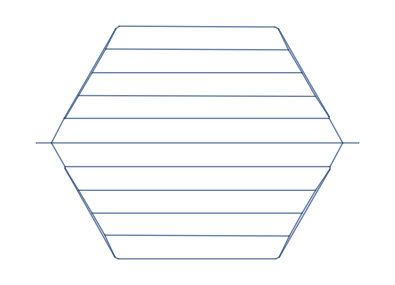

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graph=MorphologicalGraph[skeleton]
```

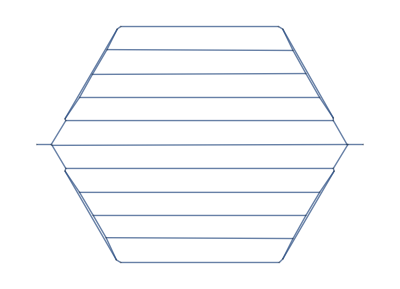

```mathematica
bin=Import["https://i.stack.imgur.com/qAZxM.png"];
g=MorphologicalGraph[bin]
```

GraphComputation`GraphContractDump`messageEdgeContract::inv: The argument 11<->14 in … is not a valid edges.

EdgeContract::graph: A graph object is expected at position 1 in ….

General::stop: Further output of EdgeContract::graph will be suppressed during this calculation.

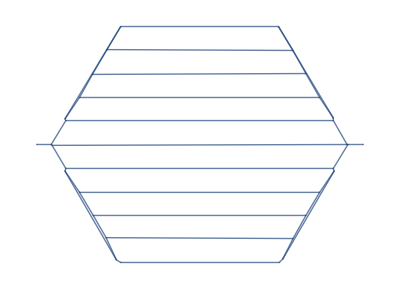
Graph[EdgeContract[EdgeContract[EdgeContract[EdgeContract[EdgeContract[EdgeContract[EdgeContract[EdgeContract[-Graphics-,11<->14],12<->13],16<->20],17<->18],21<->23],22<->24],31<->34],32<->33],VertexSize→0.2,VertexLabels→Automatic,ImageSize→600,VertexCoordinates→{v_:>vC[v]}]

```mathematica
vC=AssociationThread[VertexList[g],GraphEmbedding[g]];

edgesToContract[threshold_]:=Select[EdgeList[g],EuclideanDistance@@(List@@#/.vC)≤threshold&]

Graph[Fold[EdgeContract,g,edgesToContract[10]],VertexSize->.2,VertexLabels->Automatic,ImageSize->600,VertexCoordinates->{v_:>vC[v]}]
```